## Tahm — PS 5 — 2025-02-04

## EIWL3 Sections 14 and 17

# Chapter 14

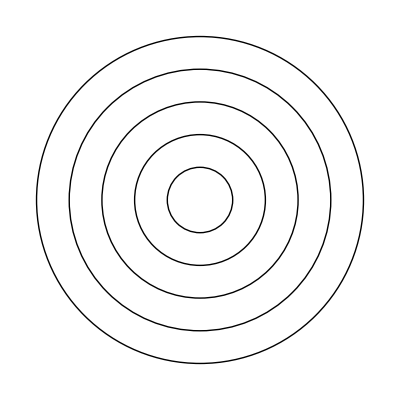

```mathematica
Graphics[Table[Circle[{1,1},x],{x,1,5}]]
```

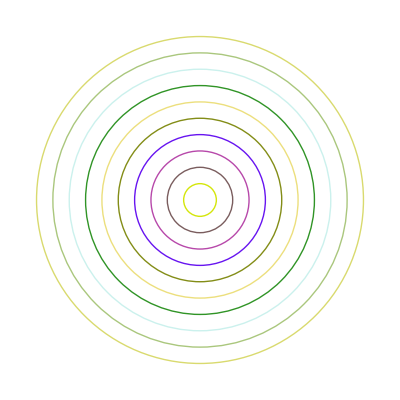

```mathematica
Graphics[Table[Style[Circle[{1,1},x],RandomColor[]],{x,1,10}]]
```

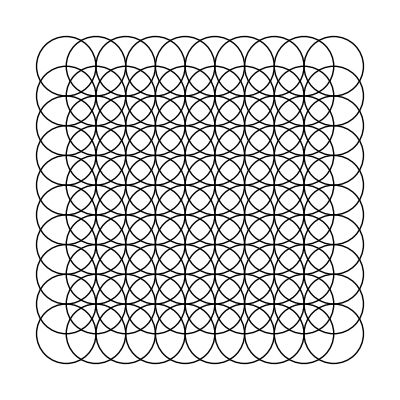

```mathematica
Graphics[Table[Circle[{x,y}],{x,1,10},{y,1,10}]]
```

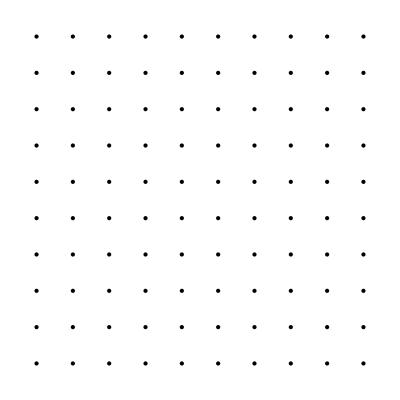

```mathematica
Graphics[Table[Point[{x,y}],{x,1,10},{y,1,10}]]
```

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{r,X}]],{X,1,20,1}]
```

```mathematica
Graphics3D[Table[Style[Sphere[{RandomInteger[10],RandomInteger[10],RandomInteger[10]}],RandomColor[]],50]]
```

-Graphics3D-

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z},0.45],RGBColor[{x/11,y/11,z/11}]],{x,0,11},{y,0,11},{z,0,11}]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,0,10}]],{t,-2,2}]
```

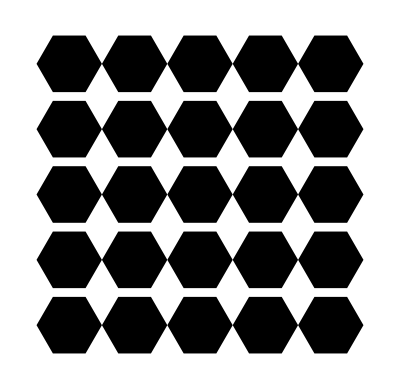

```mathematica
Graphics[Table[RegularPolygon[{x,y},1/2,6],{x,1,5},{y,1, 5}]]
```

```mathematica
Graphics3D[Line[Table[RandomInteger[50],50,3]]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[Style[{Dodecahedron[{0,0},1],Icosahedron[{0,0,0},x]},Opacity[0.5]]], {x,1,2}]
```

# Chapter 17

```mathematica
UnitConvert[4.5 Quantity[, "Pounds"],Quantity[, "Kilograms"]]
```

2.04117 kg

```mathematica
UnitConvert[60.24 Quantity[, ("Miles")/("Hours")],Quantity[, ("Kilometers")/("Hours")]]
```

96.9469 km/h

```mathematica
UnitConvert[1083.0 Quantity[, "Feet"],Quantity[, "Miles"]]
```

0.205114 mi

```mathematica
Quantity[29032., "Feet"]/Quantity[1083, "Feet"]
```

26.807

```mathematica
Quantity[5.972*^24, "Kilograms"]/Quantity[7.3*^22, "Kilograms"]
```

81.8082

```mathematica
CurrencyConvert[Quantity[2500., "Yen"],Quantity[, "USDollars"]]
```

16.28 $

```mathematica
UnitConvert[{Quantity[35, "Ounces"]+Quantity[0.25, "ShortTons"]+Quantity[45, "Pounds"]+Quantity[9, "Stones"]},Quantity[, "Kilograms"]]
```

{305.353 kg}

```mathematica
UnitConvert[EntityClass["Planet",All]["DistanceFromEarth"],"LightMinutes"]
```

{11.4146 light minutes,3.65946 light minutes,0. light minutes,6.20101 light minutes,39.2473 light minutes,87.3858 light minutes,162.496 light minutes,255.377 light minutes}

```mathematica
Rotate["hello",Quantity[180, "AngularDegrees"]]
```

hello

```mathematica
Table[Rotate[Style["A",100],x Degree],{x,0,360,30}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

```mathematica
Manipulate[Rotate["CAT",x Degree],{x,0,180}]
```

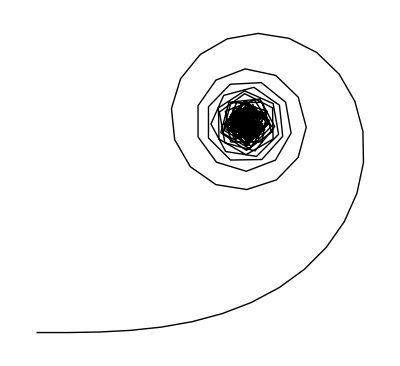

```mathematica
Graphics[Line[AnglePath[Table[x Degree, {x,0 ,180 }]]]]
```

```mathematica
Manipulate[ Graphics[Line[AnglePath[Table[x,100]]]],{x,0,360}]
```

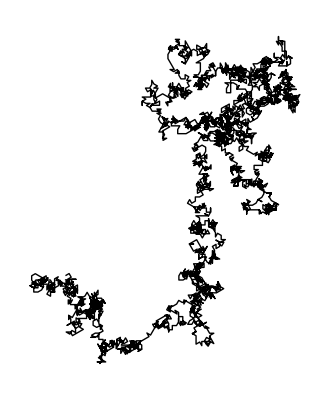

```mathematica
Graphics[Line[AnglePath[Quantity[30, "AngularDegrees"]*IntegerDigits[2^10000]]]]
```